```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
tab=Import["spectraldata/Tscan/Debye/cc/swccT162lspectra.dat"];
```

```mathematica
tab1=Import["spectraldata/Tscan/Debye/cc/swccT159lspectra.dat"];
```

```mathematica
tab=tab/.{a_,b_}:>{a,-b};
```

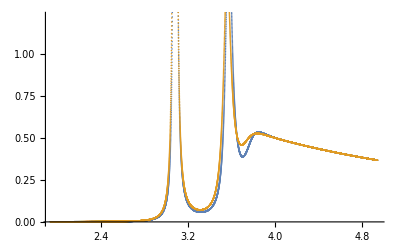

```mathematica
ListPlot[{tab1,tab}]
```

```mathematica
tab[[;;10]]
```

{{1.93838,-0.00123383},{1.93867,-0.00123414},{1.93897,-0.00123448},{1.93926,-0.0012348},{1.93955,-0.00123513},{1.93985,-0.00123545},{1.94014,-0.00123577},{1.94044,-0.0012361},{1.94073,-0.00123643},{1.94102,-0.00123675}}